```mathematica
coords=Table[Random[],{10},{2}]
```

{{0.561154,0.0744741},{0.181445,0.0434377},{0.378119,0.611969},{0.438907,0.214465},{0.416749,0.511175},{0.627681,0.6922},{0.212839,0.863133},{0.946705,0.592174},{0.510365,0.24539},{0.324463,0.392328}}

```mathematica
points=Map[Point,coords]
```

{Point[{0.561154,0.0744741}],Point[{0.181445,0.0434377}],Point[{0.378119,0.611969}],Point[{0.438907,0.214465}],Point[{0.416749,0.511175}],Point[{0.627681,0.6922}],Point[{0.212839,0.863133}],Point[{0.946705,0.592174}],Point[{0.510365,0.24539}],Point[{0.324463,0.392328}]}

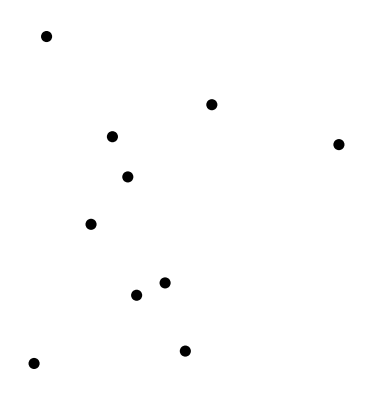

```mathematica
Show[Graphics[{PointSize[.02],points}]]
```

```mathematica
lines=Line[coords]
```

Line[{{0.561154,0.0744741},{0.181445,0.0434377},{0.378119,0.611969},{0.438907,0.214465},{0.416749,0.511175},{0.627681,0.6922},{0.212839,0.863133},{0.946705,0.592174},{0.510365,0.24539},{0.324463,0.392328}}]

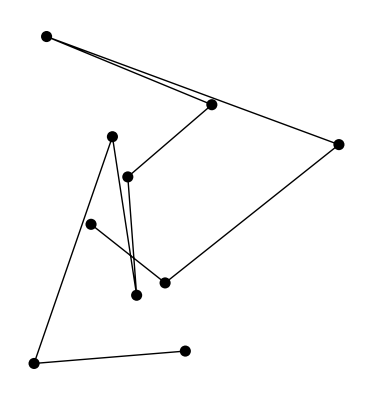

```mathematica
Show[Graphics[{PointSize[.02],points,lines}]]
```

```mathematica
path=Line[coords/.{a_,b__}->{a,b,a}];
```

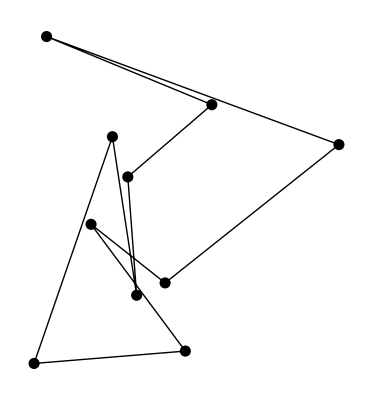

```mathematica
Show[Graphics[{PointSize[.02],points,path}]]
```

```mathematica
base=coords[[Random[Integer,{1,Length[coords]}]]]
```

{0.378119,0.611969}

```mathematica
angle[a_List,b_List]:=Apply[ArcTan,(b-a)]
```

```mathematica
remain=Complement[coords,{base}];
```

```mathematica
Map[angle[base,#]&,remain]
```

{-1.90384,2.15281,-1.81039,-1.2048,-1.41905,-1.22457,-1.24258,0.311053,-0.0348008}

```mathematica
s=Sort[remain,(angle[base,#1]≤angle[base,#2])&]
```

{{0.181445,0.0434377},{0.324463,0.392328},{0.438907,0.214465},{0.561154,0.0744741},{0.510365,0.24539},{0.416749,0.511175},{0.946705,0.592174},{0.627681,0.6922},{0.212839,0.863133}}

```mathematica
p=Join[{base},s,{base}]
```

{{0.378119,0.611969},{0.181445,0.0434377},{0.324463,0.392328},{0.438907,0.214465},{0.561154,0.0744741},{0.510365,0.24539},{0.416749,0.511175},{0.946705,0.592174},{0.627681,0.6922},{0.212839,0.863133},{0.378119,0.611969}}

```mathematica
path=Line[p];
```

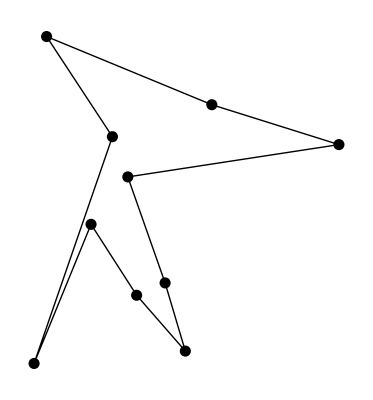

```mathematica
Show[Graphics[{PointSize[.02],points,path}]]
```

```mathematica
simpleClosedPath[l_]:=
Module[{points,base,angle,sorted,path},
points={PointSize[.02],RGBColor[1,0,0],Map[Point,l]};
base=l[[Random[Integer,{1,Length[l]}]]];
angle[a_,b_]:=Apply[ArcTan,(b-a)];
sorted=Sort[Complement[l,{base}],
(angle[base,#1]≤angle[base,#2])&];
path=Line[Join[{base},sorted,{base}]];
Show[Graphics[{{RGBColor[1,0,0],points},path}]]]
```

```mathematica
data=Table[Random[],{25},{2}];
```

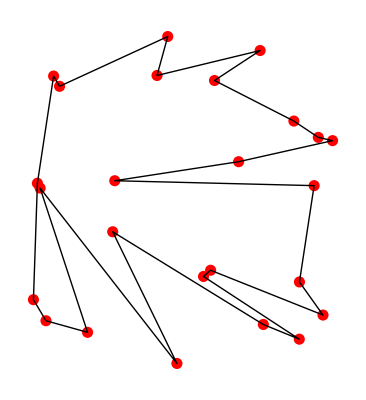

```mathematica
simpleClosedPath[data]
```

```mathematica
data=Table[Random[],{100},{2}];
```

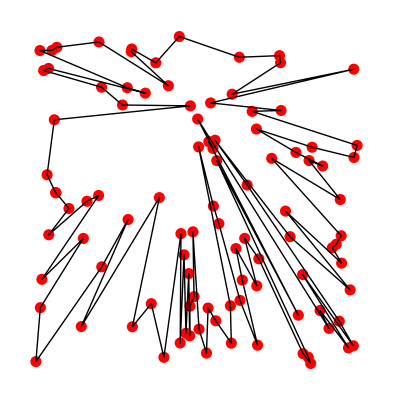

```mathematica
simpleClosedPath[data]
```

```mathematica
placeTree[{_}]:={{},0,0}
placeTree[{_,lc_,rc_}]:=
Module[{left=placeTree[lc],right=placeTree[rc],
minsep=1.0},
Module[{sep=left[[3]]+right[[2]]+minsep},
{{sep,left[[1]],right[[1]]},
left[[2]]+sep/2,right[[3]]+sep/2}]]
```

```mathematica
drawSepTree[{},lev_,xaxis_]:={Disk[{xaxis,lev},0.1]}
drawSepTree[{sep_,lc_,rc_},lev_,xaxis_]:=
Join[{Disk[{xaxis,lev},0.1],
Line[{{xaxis,lev},{xaxis-sep,lev-1}}],
Line[{{xaxis,lev},{xaxis+sep,lev-1}}]},
drawSepTree[lc,lev-1,xaxis-sep],
drawSepTree[rc,lev-1,xaxis+sep]]
```

```mathematica
showTree[tree_]:=
Show[Graphics[drawSepTree[placeTree[tree][[1]],0,0]]]
```

```mathematica
tree1={a,{b},{a,{c,{e,{g},{f}},{d}},{b}}}
```

{a,{b},{a,{c,{e,{g},{f}},{d}},{b}}}

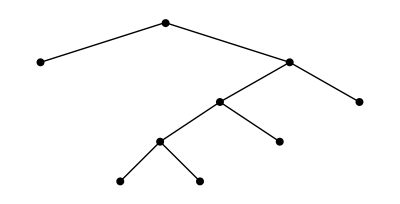

```mathematica
showTree[tree1]
```

```mathematica
simpleClosedPath[l_]:=
Module[{points,base,angle,sorted,path},
points={PointSize[.02],RGBColor[1,0,0],
Map[Point,l]};
base=Last[Sort[l,(#2[[2]]<#1[[2]])&]];
angle[a_,b_]:=Apply[ArcTan,(b-a)];
sorted=Sort[Complement[l,{base}],
(angle[base,#1]≤angle[base,#2])&];
path=Line[Join[{base},sorted,{base}]];
Show[Graphics[{{RGBColor[1,0,0],points},path}]]]
```

```mathematica
pts=Table[Random[],{20},{2}];
```

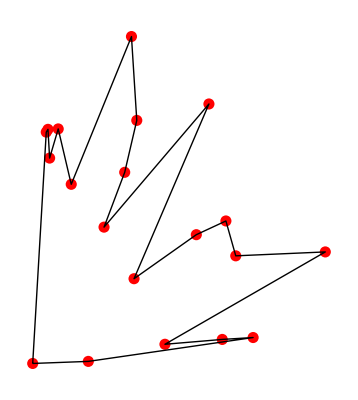

```mathematica
simpleClosedPath[pts]
```

```mathematica
simpleClosedPath[l_]:=
Module[{points,base,angle,sorted,path},
points={PointSize[.02],RGBColor[1,0,0],
Map[Point,l]};
base=Last[Sort[l,(#2[[2]]>#1[[2]])&]];
angle[a_,b_]:=Apply[ArcTan,(b-a)];
sorted=Sort[Complement[l,{base}],
(angle[base,#1]≤angle[base,#2])&];
path=Line[Join[{base},sorted,{base}]];
Show[Graphics[{{RGBColor[1,0,0],points},path}]]]
```

```mathematica
CrossProduct[{x2,y2}-{x1,y1},{x3,y3}-{x1,y1}]/.
{x_,y_}->{x,y,0}
```

CrossProduct[{-x1+x2,-y1+y2,0},{-x1+x3,-y1+y3,0}]

```mathematica
a={0,0};
b={5,0};
c={3,2};
```

```mathematica
CrossProduct[(b-a),(c-a)]/.{x_,y_}->{x,y,0}
```

CrossProduct[{5,0,0},{3,2,0}]

```mathematica
Apply[Plus,%]/2
```

{4,1,0}

```mathematica
triangleArea[v_List]:=1/2Plus@@
(Cross[v[[2]]-v[[1]],v[[3]]-v[[]]]/.
{x_,y_}->{x,y,0})
```

```mathematica
triangleArea[{v1_,v2_,v3_}]:=
Det[{v1,v2,v3}/.{x_,y_}->{x,y,1}]/2
```

```mathematica
triangleArea[{a,b,c}]
```

5

```mathematica
pointInPolygonQ[p_,poly_]:=Module[{leftofQ},
leftofQ[{v1_,v2_,v3_}]:=Det[{v1,v2,v3}/.
{x_,y_}->{x,y,1}]/2≥0;
Apply[And,Map[leftofQ[Join[{p},#]]&,
Partition[poly/.
{a_,b__}:>{a,b,a},2,1]]
]]
```

```mathematica
quad={{1,0},{0,1},{-1,0},{0,-1}};
```

```mathematica
p1={0,0};
```

```mathematica
p2={1,1};
```

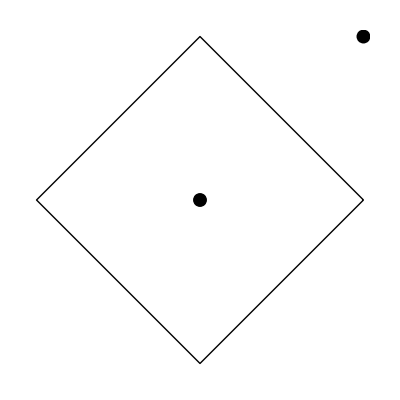

```mathematica
Show[Graphics[{Line[quad/.{a_,b__}:>{a,b,a}],
PointSize[.025],Point[p1],Point[p2]},
AspectRatio->Automatic]]
```

```mathematica
pointInPolygonQ[p1,quad]
```

True

```mathematica
pointInPolygonQ[p2,quad]
```

False

```mathematica
RT[{_}]:={{},{},{}}
RT[{_,lc_,rc_}]:=
With[{left=RT[lc],
right=RT[rc],
minsep=2.0},
With[{sep=(Max[0,Apply[Max,Map[Apply[Plus,#]&,
zip[left[[3]],right[[2]]]]]]+minsep)/2},
With[{newtree={sep,left[[1]],right[[1]]},
leftedge=Join[{sep},extend[left[[2]],
right[[2]],sep]],
rightedge=Join[{sep},extend[right[[3]],
left[[3]],sep]]},
{newtree,leftedge,rightedge}]]]
drawTree[t_]:=drawSepTree[RT[t][[1]],0,0]
zip[{},_]:={}
zip[_,{}]:={}
zip[{x1_,y1___},{x2_,y2___}]:=
Join[{{x1,x2}},zip[{y1},{y2}]]
extend[edges1_,edges2_,sep_]:=
Join[edges1+sep,Take[edges2,
Min[0,Length[edges1]-Length[edges2]]]-sep]
```

```mathematica
t1={a,{b},{a,{c,{e,{g},{f}},{d}},{b}}}
```

{a,{b},{a,{c,{e,{g},{f}},{d}},{b}}}

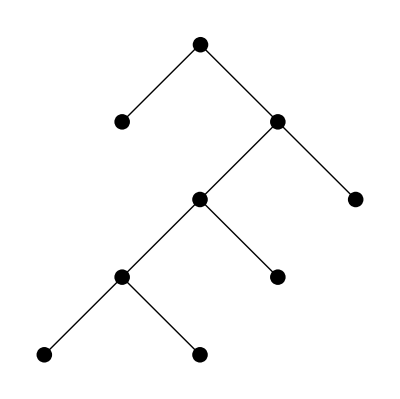

```mathematica
Show[Graphics[drawTree[t1]],
PlotRange->All,
AspectRatio->Automatic]
```

```mathematica
RT[{x_}]:={{},{width[x]/2},{width[x]/2}}
RT[{x_,lc_,rc_}]:=
With[{left=RT[lc],
right=RT[rc],
minsep=0.5},
With[{sep=(Max[0,Apply[Max,Map[Apply[Plus,#]&,
zip[left[[3]],right[[2]]]]]]+minsep)/2},
With[{newtree={sep,left[[1]],right[[1]]},
leftedge=Join[{width[x]/2},
extend[left[[2]],right[[2]],sep]],
rightedge=Join[{width[x]/2},
extend[right[[3]],left[[3]],sep]]},
{newtree,leftedge,rightedge}]]]
width[t_]:=StringLength[t]
```

```mathematica
t1={"a",{"abcdef"},{"",{"abcdefghij"},{"abc"}}}
```

{a,{abcdef},{,{abcdefghij},{abc}}}

```mathematica
settext[lab_]:=FontForm[lab,{"Helvetica",10}]
```

```mathematica
drawSepTree[{lab_},{},lev_,xaxis_]:=
{Text[settext[lab],{xaxis,lev}]}
```

```mathematica
drawSepTree[{lab_,lc_,rc_},{sep_,ls_,rs_},lev_,xaxis_]:=
With[{h1=If[lab=="",0,.3],
h2=If[lc[[1]]=="",0,.3],
h3=If[rc[[1]]=="",0,.3]},
Join[{Text[settext[lab],{xaxis,lev}],
Line[{{xaxis-sep*(h1/2),lev-h1/2},
{xaxis-sep+sep*(h2/2),lev-1+h2/2}}],
Line[{{xaxis-sep*(h1/2),lev-h1/2},
{xaxis+sep-sep*(h3/2),lev-1+h3/2}}]},
drawSepTree[lc,ls,lev-1,xaxis-sep],
drawSepTree[rc,rs,lev-1,xaxis+sep]]]
```

```mathematica
drawTree[t_]:=drawSepTree[t,RT[t][[1]],0,0]
```

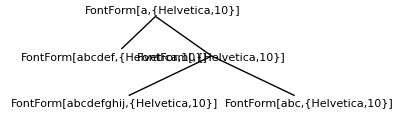

```mathematica
Show[Graphics[drawTree[t1]],PlotRange->All]
```